0.0001275

√((0.+74.8951 ⅈ) ω)

0.00551705

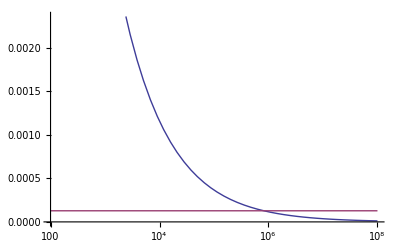

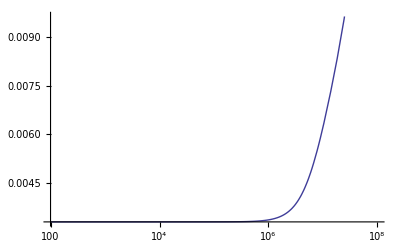

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

Plot::exclul: {Im[√(0.  + 74.8951\ ⅈ)\ ⅇ^ω\ BesselI[0, 0.0001275\ √Times[« 2 »]]/BesselI[1, 0.0001275\ Power[« 2 »]]] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0} must be a list of equalities or real-valued functions.

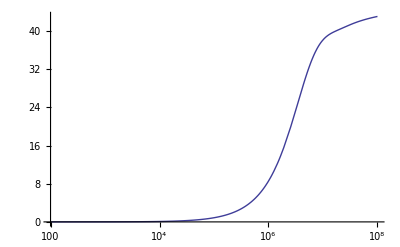

```mathematica
r = .255*10^(-3)/2
l= .01;
σ = 5.96*10^7;
μ = 1.2566290*10^-6 ;
m = Sqrt[I*ω*σ*μ]
Abs[BesselI[1,Sqrt[I*100*σ*μ]*r]]
LogLinearPlot[{1/Abs[m],r},{ω,100,100*10^6}]
LogLinearPlot[Abs[Sqrt[I*ω*σ*μ]*l*BesselI[0,Sqrt[I*ω*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*ω*σ*μ]*r])],{ω,100,100*10^6}]
LogLinearPlot[Arg[Sqrt[I*ω*σ*μ]*l*BesselI[0,Sqrt[I*ω*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*ω*σ*μ]*r])]/Degree,{ω,100,100000000}]
```

```mathematica
LogLinearPlot[Arg[Sqrt[I*ω*σ*μ]*l*BesselI[0,Sqrt[I*ω*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*ω*σ*μ]*r])],{ω,100,100*10^6}]
```

-Graphics-

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

Plot::exclul: {Im[√(0.  + 74.8951\ ⅈ)\ ⅇ^ω\ BesselI[0, 0.0001275\ √Times[« 2 »]]/BesselI[1, 0.0001275\ Power[« 2 »]]] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0, Im[(0.  + 74.8951\ ⅈ)\ ⅇ^ω] - 0} must be a list of equalities or real-valued functions.

-Graphics-